```mathematica
KEYWORD="bird"
```

bird

```mathematica
rawTranslations = KeyValueMap[#1->First[#2]&,WordTranslation[KEYWORD, All]];
```

```mathematica
Iconize[rawTranslations]
```

```mathematica
translatedList = Transliterate[Values[rawTranslations]];
translatedList=ToLowerCase[Select[translatedList,StringMatchQ[#,CharacterRange["A","z"]..]&]]
```

{niao,paksi,pajaro,ptica,burung,passaro,pakhi,tayr,burung,qin,oiseau,vogel,prndh,manuk,kus,paksi,paksi,sae,nk,uccello,niao,ndege,pasi,ptak,ptah,tsuntsu,niao,paksi,paksi,paksi,niao,pnchhy,manuk,cidaiya,qus,pasare,ibon,vogel,pky,langgam,nunu,caro,madar,pankharu,sonndu,ciriya,shimbir,pouli,ptica,vtak,shiri,prndh,roeg,inyoni,mbalame,usel,ptuska,ptica,fagel,anomaa,billit,icinyoni,intaka,pispis,ndeke,ocell,kos,buruang,gus,prica,cede,voel,fugl,nyoni,lintu,zypwr,vtak,inyoni,fugl,janavara,nonyane,txori,prinveli,nonyana,picc,gamgam,xinyenyana,paxaro,pwygl,cymcyk,paukstis,cicem,taritiet,curoize,birdo,ptic,kajak,inyoni,ptica,enyoni,inyoni,putns,manupuna,kayuni,ikwenye,bhkangala,evn,lind,eun,tshinoni,idum,lluta,nkeenyi,zwazo,onuan,niie,qus,ndeke,inuen,pispis,ghasfur,manu,auceu,lebac,fugl,para,tsidii,kus,ficin,fiutk,yel,hus,nyunyi,fuglur,ekinyonyi,utsche,degi,kutkut,gatle,paksi,guyra,niecen,hoshi,wanik,kajyk,kwenti,pidong,foosi}

```mathematica
originalPopulation = translatedList
```

{niao,paksi,pajaro,ptica,burung,passaro,pakhi,tayr,burung,qin,oiseau,vogel,prndh,manuk,kus,paksi,paksi,sae,nk,uccello,niao,ndege,pasi,ptak,ptah,tsuntsu,niao,paksi,paksi,paksi,niao,pnchhy,manuk,cidaiya,qus,pasare,ibon,vogel,pky,langgam,nunu,caro,madar,pankharu,sonndu,ciriya,shimbir,pouli,ptica,vtak,shiri,prndh,roeg,inyoni,mbalame,usel,ptuska,ptica,fagel,anomaa,billit,icinyoni,intaka,pispis,ndeke,ocell,kos,buruang,gus,prica,cede,voel,fugl,nyoni,lintu,zypwr,vtak,inyoni,fugl,janavara,nonyane,txori,prinveli,nonyana,picc,gamgam,xinyenyana,paxaro,pwygl,cymcyk,paukstis,cicem,taritiet,curoize,birdo,ptic,kajak,inyoni,ptica,enyoni,inyoni,putns,manupuna,kayuni,ikwenye,bhkangala,evn,lind,eun,tshinoni,idum,lluta,nkeenyi,zwazo,onuan,niie,qus,ndeke,inuen,pispis,ghasfur,manu,auceu,lebac,fugl,para,tsidii,kus,ficin,fiutk,yel,hus,nyunyi,fuglur,ekinyonyi,utsche,degi,kutkut,gatle,paksi,guyra,niecen,hoshi,wanik,kajyk,kwenti,pidong,foosi}

```mathematica
similarityScore[str_,wordList_]:=Mean[CosineDistance[net[str][[1]],net[#][[1]]]&/@wordList]
fitnessFunction[str_]:=-similarityScore[str,originalPopulation]

randomWord[]:=StringJoin@RandomChoice[CharacterRange["a","z"],RandomInteger[{3,5}]]

crossover[w1_,w2_]:=Module[{p=RandomInteger[{1,Min[StringLength[w1],StringLength[w2]]}]},StringJoin[StringTake[w1,p],StringDrop[w2,p]]]

mutate[word_,rate_:0.3]:=StringJoin@Map[If[RandomReal[]<rate,RandomChoice[CharacterRange["a","z"]],#]&,Characters[word]]
```

```mathematica
fitnessFunction["ogp"]
```

-237/53

```mathematica
evolveWords[populationSize_:100,generations_:50]:=Module[{population,scores,selected,newPop,bestWord,bestScore},population=Table[randomWord[],{populationSize}];
Do[scores=fitnessFunction/@population;
bestWord=First@SortBy[population,fitnessFunction];
bestScore=Max[scores];
Print["Generation ",gen,": Best word = \"",bestWord,"\" | Score = ",bestScore];
selected=Ordering[scores,-populationSize];
newPop=Table[With[{p1=population[[selected[[RandomInteger[{1,populationSize}]]]]],p2=population[[selected[[RandomInteger[{1,populationSize}]]]]]},mutate[crossover[p1,p2]]],{populationSize}];
population=newPop;,{gen,generations}];
First@SortBy[population,fitnessFunction]]
```

```mathematica
best = evolveWords[10,10]//Timing
```

Generation 1: Best word = "zygzw" | Score = -231/53

Generation 2: Best word = "chorezw" | Score = -710/159

Generation 3: Best word = "islukakpi" | Score = -650/159

Generation 4: Best word = "auhluzeotkpi" | Score = -234/53

Generation 5: Best word = "rzesgiaisjft" | Score = -737/159

Generation 6: Best word = "chirassvainjft" | Score = -272/53

Generation 7: Best word = "wazasoziastsjflyn" | Score = -859/159

Generation 8: Best word = "vaprzwastkaakssaisuhksyn" | Score = -324/53

Generation 9: Best word = "awpagoagresvaozisav" | Score = -314/53

Generation 10: Best word = "awpagotrgtaesvatozrasisv" | Score = -1078/159

{0.023,dpaksaatrtruhawghaoeugapaavop}

```mathematica
net=NetModel["GloVe 300-Dimensional Word Vectors Trained on Common Crawl 840B"]
```

```mathematica
EmbeddingLayer[<>]
```

EmbeddingLayer::noinfo: Input expression EmbeddingLayer[<>] contains insufficient information to interpret as input.

```mathematica
positionedDigrams=Flatten[Table[If[StringLength[word]>=pos+1,{pos,StringTake[word,{pos,pos+1}]},Nothing],{word,translatedList},{pos,StringLength[word]-1}],1];
groupedByPosition=GroupBy[positionedDigrams,First->Last];
countsByPosition=AssociationMap[Counts[groupedByPosition[#]]&,Keys[groupedByPosition]];
topDigramsByPosition=Table[Keys@TakeLargestBy[countsByPosition[pos],Identity,UpTo[5]],{pos,Sort@Keys[countsByPosition]}];
SYLLABLECOUNT=Round[Mean[Length/@(ResourceFunction["WordSyllables"][#]&/@translatedList)]]
```

2

```mathematica
Flatten[topDigramsByPosition]
```

{pa,pt,ni,in,ma,ak,an,us,ti,ny,ks,ic,nu,yo,ao,si,on,ca,ar,el,ni,ng,an,ro,am,on,ar,ro,lo,su,ni,ru,ra,li,ya,an,la,yi,na}

```mathematica
generateWord[]:=Module[{numSyllables,selectedLists,syllables},numSyllables:=RandomInteger[{SYLLABLECOUNT, SYLLABLECOUNT+2}];
selectedLists=Take[topDigramsByPosition,numSyllables];
syllables=RandomChoice/@selectedLists;
StringJoin[syllables]]
Table[generateWord[],{10}]
```

{ptnynu,pttiicon,intinuon,maanks,maanks,ninyyo,inanic,maanyo,patiyo,maan}

```mathematica
words = translatedList;
charSet=Flatten[topDigramsByPosition];


fitnessFunction[candidate_String]:=-Mean[EditDistance[candidate,#]&/@words];


randomString[]:=StringJoin@RandomChoice[Flatten[topDigramsByPosition],RandomInteger[{SYLLABLECOUNT, SYLLABLECOUNT+2}]];

populationSize=100;
generations=500;
mutationRate=0.2;

population=Table[randomString[],{populationSize}]

Do[
fitnesses=fitnessFunction/@population;
bestFitness=Max[fitnesses];
bestCandidate=population[[First@Ordering[fitnesses,-1]]];
parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
crossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
chars1=Characters[p1];
chars2=Characters[p2];
StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];
mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];

children=Table[mutate@crossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];

population=children;

,{gen, 1 , generations}];

bestWord=First@MaximalBy[population,fitnessFunction]
fitnessFunction[bestWord]
```

{paning,ranu,yinima,akanonpt,nucaptng,icpaon,ptroicon,niro,rayiks,onar,yosusiao,caarsu,amam,ruyi,timapt,laarrony,raic,mangma,icliyo,arru,yoca,yoarlaru,arpt,nysuakng,tielyo,annalo,onon,elaryi,ansuaksu,ning,ksanak,ninyao,licaello,caruna,yiusngsu,aoamonan,ksru,arruro,icloarni,anraar,usngpa,elar,rangsuro,nitiak,anng,icyarola,lisi,losiny,aolo,aknaaoel,amsuniti,tiksus,anamyaya,raonmaon,icon,lainniyi,yani,akaoonic,arca,annuna,ptaksinu,roloonng,singnyin,ancaptin,siyama,amcaling,nitiam,onon,caloonna,lora,tiarpt,yicaicin,anyo,royicani,iclana,sinuti,onmaar,lacaru,nisu,ksakksyi,ruroonng,ksla,liarniar,siakks,yinuroro,inan,marusini,arni,rana,ananak,ngrousin,ksroruli,pticinin,sicainni,kscang,nisunusu,yoan,loan,roroan,akngroel}

pani

-157/37

pana

-319/74

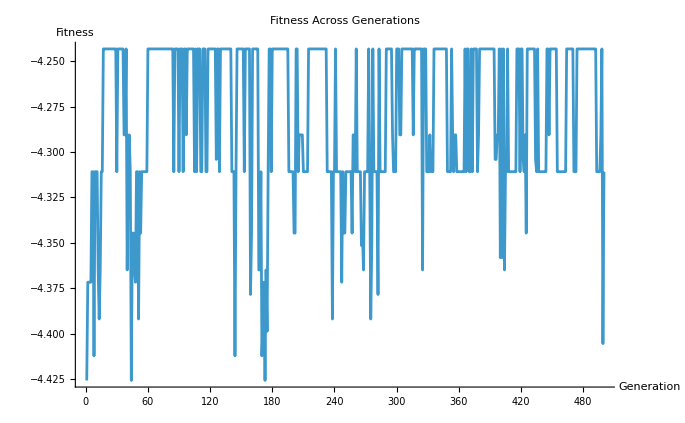

```mathematica
populationSize=100;
generations=500;
mutationRate=0.2;

population=Table[randomString[],{populationSize}];

fitnessValues={}; (* List to store fitness values *)

Do[
  fitnesses=fitnessFunction /@ population;
  bestFitness=Max[fitnesses];
  bestCandidate=population[[First@Ordering[fitnesses,-1]]];
  AppendTo[fitnessValues,bestFitness];
  parents=TakeLargestBy[Transpose[{population,fitnesses}],Last,Ceiling[populationSize/2]][[All,1]];
  crossover[p1_,p2_]:=Module[{len,chars1,chars2},len=Min[StringLength[p1],StringLength[p2]];
    chars1=Characters[p1];
    chars2=Characters[p2];
    StringJoin@Table[RandomChoice[{chars1[[i]],chars2[[i]]}],{i,1,len}]];
  mutate[str_]:=StringJoin@Table[If[RandomReal[]<mutationRate,RandomChoice[charSet],c],{c,Characters[str]}];

  children=Table[mutate@crossover[RandomChoice[parents],RandomChoice[parents]],{populationSize}];

  population=children;

,{gen,1,generations}];

bestWord=First@MaximalBy[population,fitnessFunction];
Print[bestWord];
Print[fitnessFunction[bestWord]];

(* Plot the fitness values *)
ListLinePlot[fitnessValues,AxesLabel->{"Generation","Fitness"},PlotLabel->"Fitness Across Generations"]
```